## Collision Detection

Functions to compute viscous motion from Craig

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },

Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Which[
index> perturbedIndex,newPositions[index-1] + Δ[[index]],
True,newPositions[index+1] + Δ[[index]]];

newPositions/@Range[Length[Δ]]
]
```

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

Initial Positions

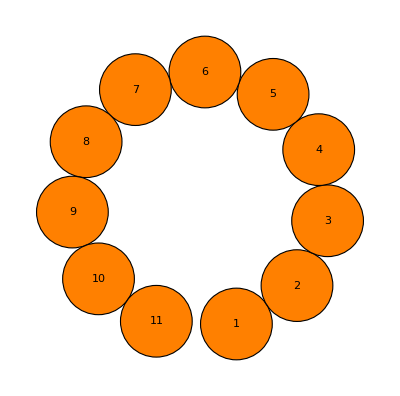

```mathematica
positions=AnglePath[ConstantArray[0.565,10]];
Graphics[chainGraphic[positions]]
```

Collision

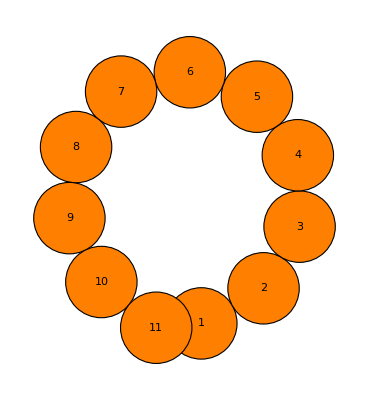

```mathematica
collisionPositions=displacements[10,positions,0.1,0,0];
collisionPositions//chainGraphic//Graphics
```

Simple Idea:

Flip/Flop until collision detection

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},
Total[Length[nf[#,{All,0.9999}]]&/@positions]]<=Length[positions]
```

```mathematica
collisionFreeDisplacements[{s_,previousCollisionTest_,previousS_}][perturbedIndex_,positionList_,ν_,θ_]:= Block[{positions,collisionTest,δs=previousS-s},

positions=displacements[perturbedIndex,positionList,s,ν,θ];
If[Abs[δs]<0.0005,Return[positions]];
collisionTest=collisionFreeQ[positions];

(*Echo[{previousCollisionTest,collisionTest,s,previousS,δs}];*)

Switch[{previousCollisionTest,collisionTest},
(*Base Case*)
{"Start",True},Return[positions],
(*Overshot, half distance*)
{"Start",False},collisionFreeDisplacements[{s+δs/2,collisionTest,s}][perturbedIndex,positionList,ν,θ],
(*Wrong Direction, half distance*)
{False,False},collisionFreeDisplacements[{s-δs/2,collisionTest,s}][perturbedIndex,positionList,ν,θ],
(*Flip-flopped, half distance and reverse*)
{False,True},collisionFreeDisplacements[{s+δs/2,collisionTest,s}][perturbedIndex,positionList,ν,θ],
(*Yet to flip-flop again, half distance*)
{True,True},collisionFreeDisplacements[{s-δs/2,collisionTest,s}][perturbedIndex,positionList,ν,θ],
(*Overshot again, half distance and reverse*)
{True,False},collisionFreeDisplacements[{s+δs/2,collisionTest,s}][perturbedIndex,positionList,ν,θ]
]
]
```

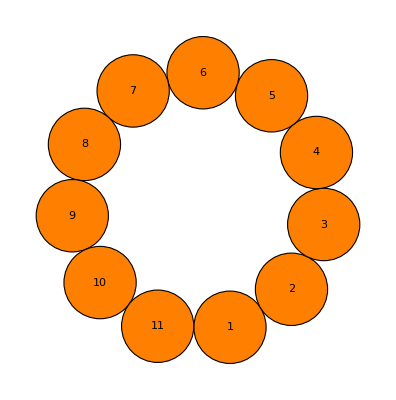

```mathematica
newPositions=collisionFreeDisplacements[{0.1,"Start",0}][10,positions,0,0];
newPositions//chainGraphic//Graphics
```

Testing it all together

```mathematica
polymerPositions = AnglePath[RandomReal[{-1,1},20]];
currentGraphic = Graphics[chainGraphic[polymerPositions],PlotRange->All,PlotRangePadding->5,Frame->True];
Dynamic[currentGraphic]
```

```mathematica
With[{stiffness = 0, relativeTemperature = 0.2},
Do[
With[{whichParticle =RandomInteger[{1,Length[polymerPositions]}],
perturbation = RandomVariate[MaxwellDistribution[relativeTemperature]],
angle = RandomReal[2Pi]
},
polymerPositions=collisionFreeDisplacements[{perturbation,"Start",0}][whichParticle,polymerPositions,stiffness,angle];
currentGraphic = Graphics[chainGraphic[polymerPositions],PlotRange->All,PlotRangePadding->5,Frame->True];
];Pause[0.05],
{1000}
]
]
```

$Aborted